```mathematica
table1 = Flatten[ImportString[Import["/Volumes/Pile/elan/Thesaurus/Mathematica/w1_degree_distributions.txt"], "Table"]];
```

```mathematica
table2 = Flatten[ImportString[Import["/Volumes/Pile/elan/Thesaurus/Mathematica/rw2_degree_distributions.txt"], "Table"]];
```

```mathematica
table3 = Take[table2,100000];
table4 = Take[table3, 10000];
```

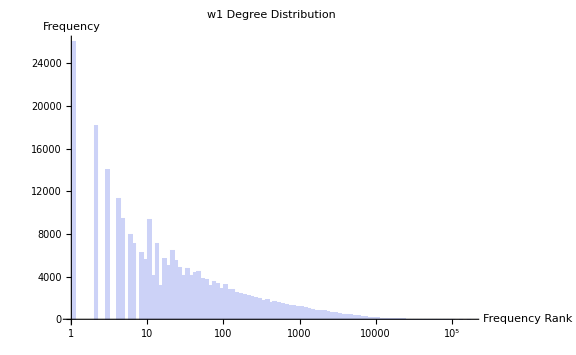

```mathematica
plot1 = Histogram[table1,{"Log",100},AxesLabel->{"Frequency Rank", "Frequency"},PlotLabel->Style["w1 Degree Distribution",Bold],ImageSize->Large]
```

```mathematica
plot2 = ListLogPlot[table2,AxesLabel->{"Frequency Rank", "Frequency"},PlotLabel->Style["rw2 Degree Distribution",Bold],ImageSize->Large]
```

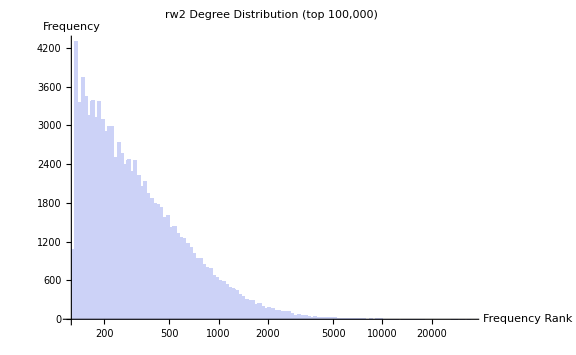

```mathematica
plot3 = Histogram[table3,{"Log",100},AxesLabel->{"Frequency Rank", "Frequency"},PlotRange->All,PlotLabel->Style["rw2 Degree Distribution (top 100,000)",Bold],ImageSize->Large]
```

```mathematica
bl=BinCounts[Log[√2,N[#]]&/@table1, {0,32,1}]
```

{26007,0,18113,14015,20774,21282,14936,14373,17161,14467,14096,11736,9818,9080,7668,6483,5870,5053,4408,3714,3274,2590,2148,1602,1190,812,461,249,108,58,19,3}

```mathematica
Log[#1,#2]& @@@{{2,4},{3,9},{10,100}}
```

{2,2,2}

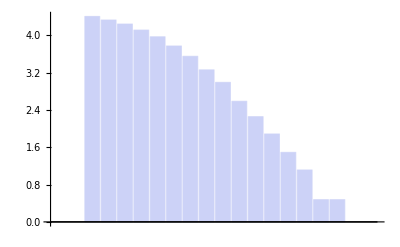

```mathematica
BarChart[Log[10,#]& /@bl]
```

```mathematica
(Table[N[√2]^n,{n,12,31,1}] bl)^2/2//Total
```

6.81476×10^13

```mathematica
Length[bl]
```

20

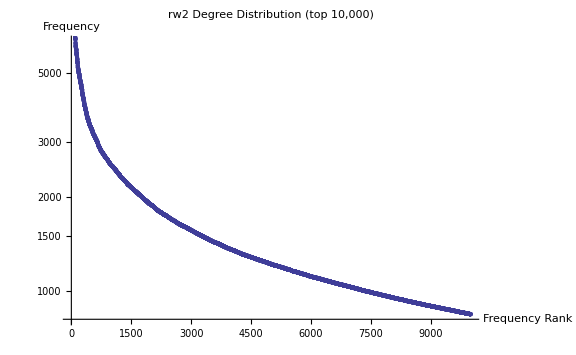

```mathematica
plot4 = ListLogPlot[table4,AxesLabel->{"Frequency Rank", "Frequency"},PlotLabel->Style["rw2 Degree Distribution (top 10,000)",Bold],ImageSize->Large]
```

```mathematica
Length[DictionaryLookup[]]
```

92518

```mathematica
DictionaryLookup[]
```

{a,Aachen,aah,Aaliyah,aardvark,aardvarks,Aaron,abaci,aback,abacus,abacuses,abaft,abalone,abalones,abandon,abandoned,abandoning,abandonment,abandons,abase,abased,abasement,abases,abash,abashed,abashedly,abashes,abashing,abashment,abasing,«92459»,Zoroastrians,Zorro,Zosma,zounds,zoundses,Zsigmondy,Zubenelgenubi,Zubeneschamali,zucchini,zucchinis,zugzwang,Zukor,Zulu,Zululand,Zulus,Zuni,Zunis,Zurich,Zürich,zwieback,Zwingli,Zworykin,zydeco,zygote,zygotes,zygotic,zymurgy,Zyrtec,Zyuganov}